Last modified on: Tuesday, July 10, 2018 at 23:37

Author Info

Katja Della Libera

Sebastian Bodenstein

Minerva Schools at KGI

Poster Session Content

Chart Identification using Machine Learning

The goal is to train a Neural Network to read charts from pictures similar to what is already possible with text recognition.
The sub-problem I am focusing on for the project is reading bar charts.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

I created a function that uses two neural networks, one reading the highest bar of the bar chart and one reading the relative heights of the bars. The biggest challenge was in the diversity of different visual representations of bar charts with mesh, background colors, etc. Over the course of the project, I generated more and more data to expand the types of graphs my network was able to read, but there are still several problems to fix.

There are many further expansion like making this network a subset of a larger network that can identify graphs, align them in the right direction and read them independent of the type.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Performance on graphs from WebImageSearch

-Graphics-
- similar performance on similar graphs
- problems recognizing the scale due to limited training set

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

The network was successful in reading many graphs of different sizes, number of bars, etc. although it needs to be trained on better data, and there are a few bugs that need fixing like the inability to read yellow or distinguish between neighboring bars of similar height.

#### Code

Importing the dataset and splitting it into a training and testing set.

```mathematica
ids=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData3.mx"];
mxs=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData3.mx"];
```

```mathematica
(*complete dataset*)
data=Flatten[Map[
	{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]
	->{Max[mxs[[Key[#]]]]}}&,ids]];
(*separate training and testing set *)
{training,testing}=TakeDrop[RandomSample[data],81000];
```

Constructing the first neural net, a modification of the VGG-16 Trained on ImageNet Competition Data. This net will be responsible for reading the highest bar of the bar chart.

```mathematica
(*Importing vgg16Net as a base for my network*)
vgg16Net= NetModel["VGG-16 Trained on ImageNet Competition Data","UninitializedEvaluationNet"]
(*cutting off a few layers at the end to match the output form I want (one number)*)
vgg16Net2= NetReplacePart[NetTake[vgg16Net,{"conv1_1","pool5"}],
"Input"->NetEncoder[{"Image",100}]];
(*Adding a BatchNormalizationLayer before every ConvolutionLayer*)
vgg16Net3=NetInsert[vgg16Net2,"b1"->BatchNormalizationLayer[],"conv1_2"];
vgg16Net3=NetInsert[vgg16Net3,"b2"->BatchNormalizationLayer[],"conv2_1"];
vgg16Net3=NetInsert[vgg16Net3,"b3"->BatchNormalizationLayer[],"conv2_2"];
vgg16Net3=NetInsert[vgg16Net3,"b4"->BatchNormalizationLayer[],"conv3_1"];
vgg16Net3=NetInsert[vgg16Net3,"b5"->BatchNormalizationLayer[],"conv3_2"];
vgg16Net3=NetInsert[vgg16Net3,"b6"->BatchNormalizationLayer[],"conv3_3"];
vgg16Net3=NetInsert[vgg16Net3,"b7"->BatchNormalizationLayer[],"conv4_1"];
vgg16Net3=NetInsert[vgg16Net3,"b8"->BatchNormalizationLayer[],"conv4_2"];
vgg16Net3=NetInsert[vgg16Net3,"b9"->BatchNormalizationLayer[],"conv4_3"];
vgg16Net3=NetInsert[vgg16Net3,"b10"->BatchNormalizationLayer[],"conv5_1"];
vgg16Net3=NetInsert[vgg16Net3,"b11"->BatchNormalizationLayer[],"conv5_2"];
vgg16Net3=NetInsert[vgg16Net3,"b12"->BatchNormalizationLayer[],"conv5_3"];
(*Adding a LinearLayer[1] as the last layer*)
vgg16Net4=NetChain[{vgg16Net3,LinearLayer[1]}]
```

Training this net on the generated data

```mathematica
vgg16NetTrained=NetTrain[vgg16Net4,training,ValidationSet->testing,
						TargetDevice->"GPU",BatchSize->32]
Export["MaxLength3.wlnet",vgg16NetTrained]
```

```mathematica
vgg16NetTrained=Import["MaxLength3.wlnet"]
```

NetChain[<>]

Creating a dataset for the relative bar chart height reader.

```mathematica
(*defining a function that takes a list of values and turns them into relative heights
to a given number of bins*)
class[list_,nbins_]:=Map[Floor[(#/Max[list])*nbins]&,list]
(*using the class function and my ids to associate each file with the list of its relative heights*)
listData=Flatten[Map[
	{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]->class[mxs[[Key[#]]],20]}&,
			ids]];
(*splitting the dataset in the same number of training and testing data as before*)
{traininglist,testinglist}=TakeDrop[RandomSample[listData],98000];
```

Creating the network of the relative bar chart height reader.

```mathematica
(*defining a few building blocks for the network*)
loss=CTCLossLayer[];
classes=Range[20];
decoder=NetDecoder[{"CTCBeamSearch",classes}];
convUnit[c_]:=NetChain[{ConvolutionLayer[c,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2]}]
(*putting the net together*)
ocrNet=NetChain[{convUnit[50],convUnit[50],convUnit[50],convUnit[50],convUnit[10],
	TransposeLayer[1<->3],FlattenLayer[-1],GatedRecurrentLayer[50],GatedRecurrentLayer[50],
	NetMapOperator[LinearLayer[Length[classes]+1]],SoftmaxLayer[]},
	"Input"->NetEncoder[{"Image",100,"Grayscale"}],"Output"->decoder]
```

Training the network

```mathematica
ocrNetTrained=NetTrain[ocrNet,traininglist,ValidationSet->testinglist,LossFunction->loss,BatchSize->32,TargetDevice->"GPU"]
Export["RelativeHeight3.wlnet",ocrNetTrained];
```

```mathematica
ocrNetTrained=Import["RelativeHeight3.wlnet"]
```

NetChain[<>]

Combining the two networks into a function that can read bar charts from images.

```mathematica
readGraph[graph_]:=Flatten[Map[#*(vgg16NetTrained[graph]/20)&,ocrNetTrained[graph]]]
SetAttributes[readGraph,Listable]
```

#### Conclusions in Detail

This project has many possible implications but the scope and accuracy so far is not much more than a proof of concept, though a promising one. I hope to further develop this technology and improve the network enough to get a reasonable accuracy.

#### All Visualizations

Performance of the first neural network, reading the highest bar of each bar chart.

```mathematica
sample=RandomSample[testing,10];
Grid[Prepend[Map[{Show[Import[#[[1]]],ImageSize->200],vgg16NetTrained[#[[1]]],#[[2]],
		((vgg16NetTrained[#[[1]]]-#[[2]])/#[[2]]*100)}&,sample],
{"Input", "Output", "expected Output","Percentage Error"}],Frame->All]
```

Input | Output | expected Output | Percentage Error
-Graphics- | {9536.33} | {9736} | {-2.05081}
-Graphics- | {8495.93} | {8452} | {0.51972}
-Graphics- | {5227.38} | {5298} | {-1.33299}
-Graphics- | {5163.74} | {5095} | {1.34913}
-Graphics- | {9094.34} | {9129} | {-0.379682}
-Graphics- | {8375.15} | {8605} | {-2.67109}
-Graphics- | {8864.53} | {8921} | {-0.632976}
-Graphics- | {9488.19} | {9706} | {-2.24407}
-Graphics- | {9633.43} | {9794} | {-1.63947}
-Graphics- | {8705.91} | {8753} | {-0.538019}

Performance of the second NN, reading the relative height of the bar charts.

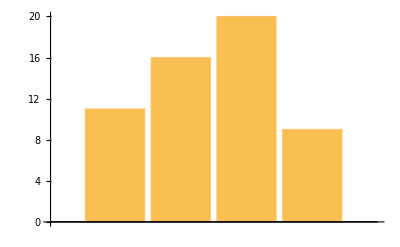
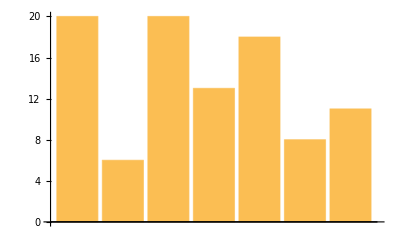
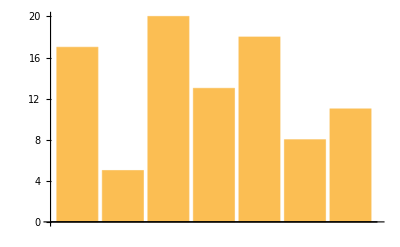
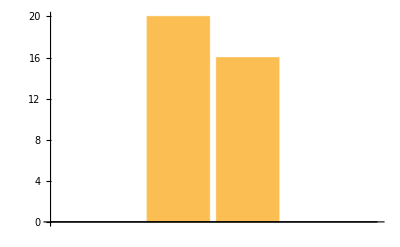
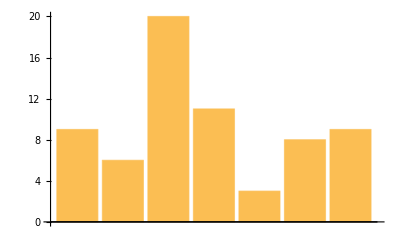
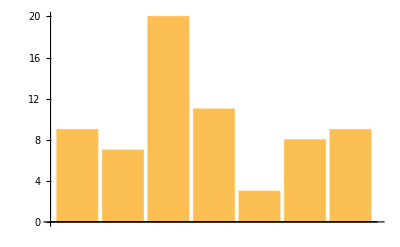
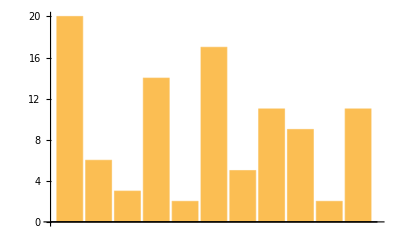
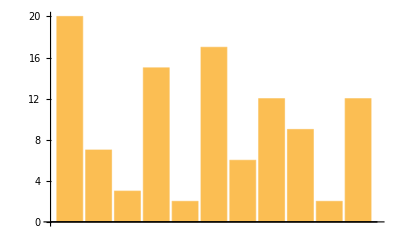
Input | Output | expected Output
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*defining a sample of the list data*)
samplelist=RandomSample[testinglist,10];
(*visually representing the output of the network reading the relative heights*)
Grid[Prepend[Map[
	{Show[Import[#[[1]]],ImageSize->200],BarChart[ocrNetTrained[#[[1]]]],BarChart[#[[2]]]}&,samplelist],
	{"Input", "Output", "expected Output"}],Frame->All]
```

Performance of the combined neural networks in reading graphs generated by the wolfram language (sample of the testing set)

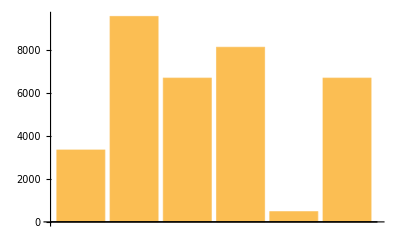
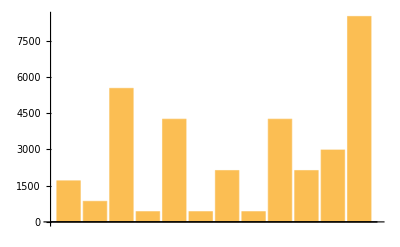
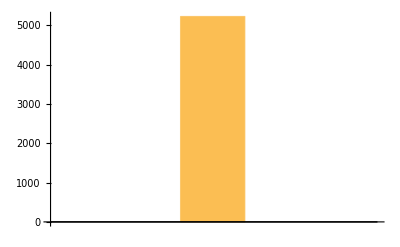
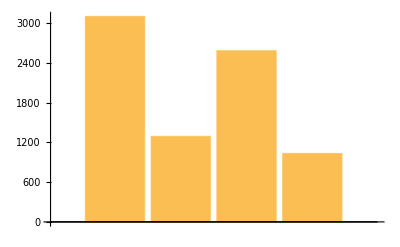
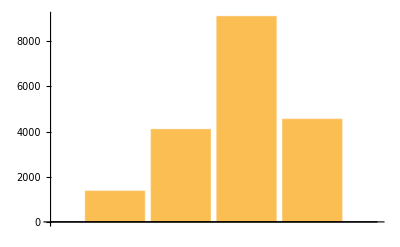
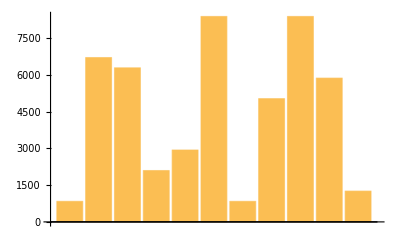
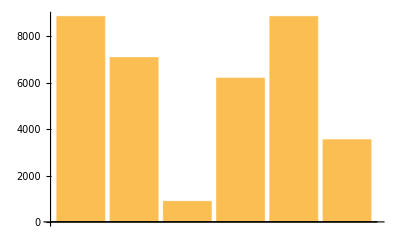
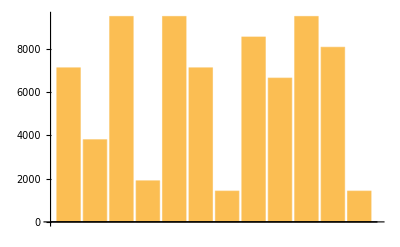
Input | Output
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Prepend[Map[{Show[Import[#],ImageSize->200],BarChart[readGraph[#]]}&,sample[[All,1]]],
	{"Input", "Output"}],Frame->All]
```

Performance of the function on graphs that were not generated, but results of a WebImageSearch

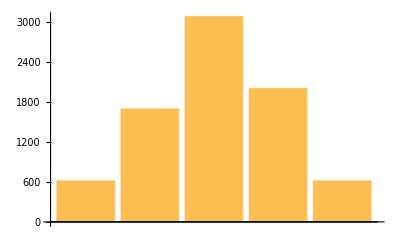
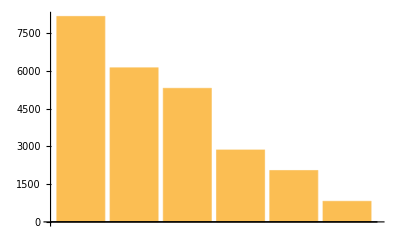
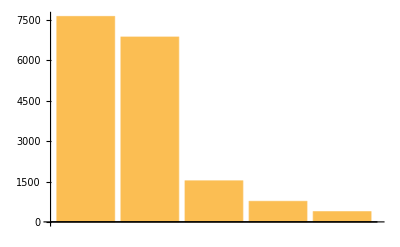
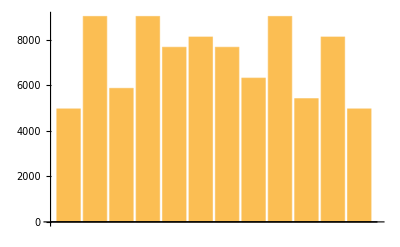
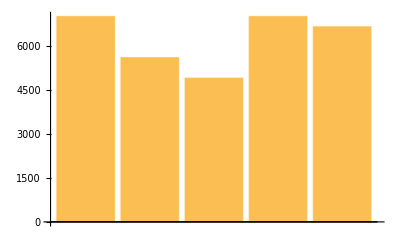
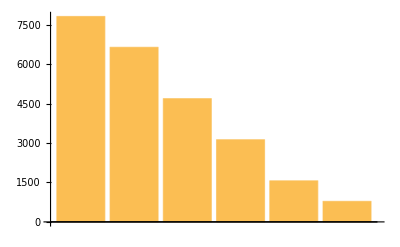
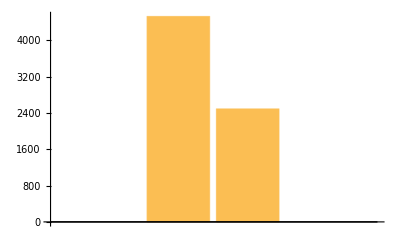
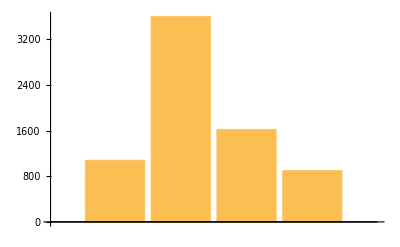
Chart | Interpretation
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Prepend[Map[{Show[#,ImageSize->200],BarChart[readGraph[#]]}&,
WebImageSearch["Bar Chart", "Thumbnails",MaxItems->100]],{"Chart","Interpretation"}],
	Frame->All]
```

#### Data Sources Links/References

Code to generate dataset of bar charts (with slight modifications for different purposes):

```mathematica
SeedRandom[123456]; 
randomList:=Table[{RandomInteger[{10000,100000}],RandomWord[]},RandomInteger[{1,15}]];

dataset= ParallelTable[With[{j=CreateUUID[],rl=randomList},
	(Export[StringTemplate["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData3\\``.jpg"][j],
	Rasterize[BarChart[
	RandomChoice[{
rl[[All,1]],
Map[Labeled[#[[1]],#[[2]]]&,rl],
Map[Placed[Labeled[#[[1]],#[[1]]],Top]&,rl]
}],
	ChartStyle->RandomChoice[ColorData["Charting"]], 
	ChartStyle->Thickness[RandomReal],
	Background->RandomChoice[{.8,.2}->{None,RandomColor[]}],
	ChartElementFunction->RandomChoice[ChartElementData["BarChart"]],
	BarSpacing->RandomChoice[{None,Automatic,Tiny,Small,Medium,Large}],
	PlotLabel->RandomChoice[WordList[]],
	PlotRange->Max[rl[[All,1]]]+RandomInteger[{0,4000}]
	],ImageSize->RandomInteger[{100,400}]]];
		Export[StringTemplate["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData3\\``.mx"][j],
		rl[[All,1]]])],5000];
```

#### Future Directions

There are several approaches with which I hope to fix some of the bugs:
Firstly, I think there is much more that this network can learn given a broader range of data, styles and directions.
Secondly, I hope to use more traditional methods, like image pre-processing, a text identifier to read labels and other functions that turn or split bar charts, etc to complement what I have done in this limited time.

#### Github repository link

https : // github.com/katjadellalibera/WolframSummerSchool2018/blob/master/Project/DellaLibera - Katja - Project.nb

#### Keywords

Machine Learning

OCR

bar charts